Yohan Lee  Lab 3

Examples

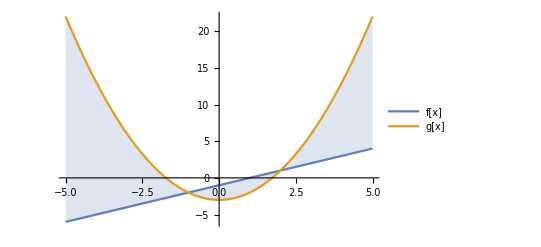

```mathematica
Clear[f,g];
f[x_] := x-1;
g[x_]:= x^2-3;
Plot[{f[x],g[x]},{x,-5,5}, Filling->{1->{2}},PlotLegends->{"f[x]","g[x]"}]
```

```mathematica
NSolve[f[x]==g[x],x]
```

{{x→-1.},{x→2.}}

```mathematica
Integrate[f[x]-g[x], {x,-1,2}]
```

9/2

```mathematica
Clear[f]
```

```mathematica
f[x_]:=Sin[x]
```

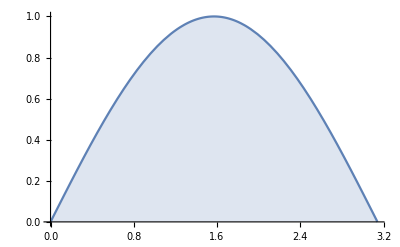

```mathematica
Plot[f[x],{x,0,Pi}, Filling->Axis]
```

```mathematica
RevolutionPlot3D[f[x],{x,0,Pi},RevolutionAxis->"x"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[f[x],{x,0,Pi}]
```

-Graphics3D-

```mathematica
Clear[f,g];
f[x_] := x-1;
g[x_]:= x^2-3;
Pi*Integrate[(3-g[x])^2 - (3-f[x])^2, {x,-1,2}]
Pi*Integrate[(3-g[x])^2 - (3-f[x])^2, {x,-1,2}]//N
```

(198 π)/5

124.407

Question 1a

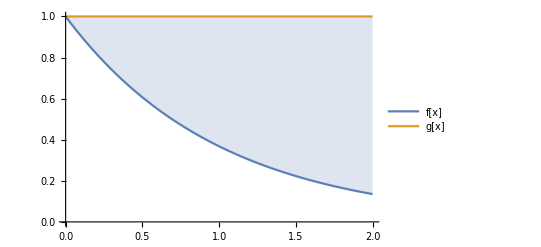

```mathematica
Clear[f,g];
f[x_]=Exp[-x];
g[x_]:= 1;
Plot[{f[x],g[x]},{x,0,2}, Filling->{1->{2}},PlotLegends->{"f[x]","g[x]"}]
```

Question 1b

```mathematica
Pi*Integrate[(2+f[x])^2-(2-1)^2, {x,0,2}]
```

(21/2-1/(2 ⅇ^4)-4/ⅇ^2) π

```mathematica
Pi*Integrate[(2-f[x])^2-(2-1)^2, {x,0,2}]//N
```

9.52588

Volume found by washer method

Question 2a

```mathematica
Clear[f,g];
f[x_] := x+7;
g[x_]:= 9-x^2;
```

```mathematica
Solve[f[x]==g[x],x]
```

{{x→-2},{x→1}}

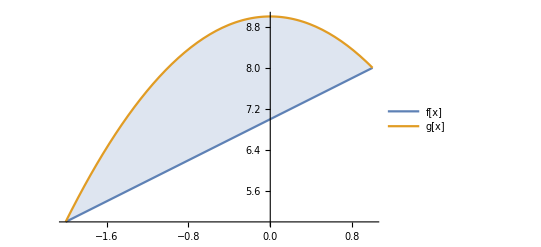

```mathematica
Plot[{f[x],g[x]},{x,-2,1}, Filling->{1->{2}},PlotLegends->{"f[x]","g[x]"}]
```

Question 2b

```mathematica
2*Pi*Integrate[(2-x)(g[x]-f[x]), {x,-2,1}]
```

(45 π)/2

```mathematica
2*Pi*Integrate[(2-x)(g[x]-f[x]), {x,-2,1}]//N
```

70.6858

Volume found using shell method